## Interesting, useful and/or correct

### Useful Actions

```mathematica
RealUnitonAction[ζ_,η_]:=((1+ζ^2+2 ζ η+η^2) ((ζ-η) ArcTan[ζ-η]-(ζ+η) ArcTan[ζ+η]))/(2 ζ η)
ComplexUnitonAction[ζ_,η_]:=(1+(η+ζ)^2)((η-ζ)ArcCot[η-ζ]-(η+ζ)ArcCot[η+ζ])/(4η ζ)
```

### Plot Machinery

```mathematica
(*Beautify representation of η and ζ*)
MakeString=Function[inputdefs,Module[{ChoppedDeformationProbes, DeformationProbesAbs, DeformationProbesArg},
ChoppedDeformationProbes= Chop[inputdefs];
If[ComplexExpand@Re[ChoppedDeformationProbes]==ChoppedDeformationProbes,
(*For real Values*)
outstring=Rationalize[ChoppedDeformationProbes],
(*For complex values*)
DeformationProbesArg=Evaluate[Rationalize[Arg[ChoppedDeformationProbes]/Pi]Pi];
DeformationProbesAbs=Evaluate[Rationalize[Abs[ChoppedDeformationProbes]]];
outstring=Table[ToString[DeformationProbesAbs[[i,j]], StandardForm]<>ToString[HoldForm[E^(ⅈ a)] /. a-> DeformationProbesArg[[i,j]], StandardForm], {i, Length[ChoppedDeformationProbes]}, {j,2}]];
outstring]];
```

```mathematica
(*Make Plots*)
MakePlot=Function[filename, 
SetDirectory[NotebookDirectory[]];
Get["Data/"<>ToString[filename]<>".m"];

DeformationsString=MakeString[DeformationProbes];

Do[
PlotPoles[i]=ListPlot[Table[{Re[PadePoles[i][[j]]], Im[PadePoles[i][[j]]]}, {j, 1, Length[PadePoles[i]]}],
PlotLabel->"η = "<>ToString[DeformationsString[[i,2]], StandardForm]<>", ζ = " <>ToString[DeformationsString[[i,1]], StandardForm]<>", k = "<>ToString[k],
PlotRange->{{-8, 8}, {-8, 8}},
PlotStyle-> {PointSize[Medium]},
ImageSize->600],
{i, 1, Length[DeformationProbes]}];

(*Draw Circles*)
DrawCircle[r_, Colour_]:=ParametricPlot[{r Cos[t], r Sin[t]}, {t, 0, 2 Pi}, PlotStyle->{Colour, Dashed}];
RealActionCircle[i_]:=DrawCircle[Abs[2 RealUnitonAction[DeformationProbes[[i,1]]+10^-10, DeformationProbes[[i,2]]+10^-10]], Red];
ComplexActionCircle[i_]:=DrawCircle[Abs[2 ComplexUnitonAction[DeformationProbes[[i,1]]+10^-10, DeformationProbes[[i,2]]+10^-10]], Green];
DoubleComplexActionCircle[i_]:=DrawCircle[Abs[4ComplexUnitonAction[DeformationProbes[[i,1]]+10^-10, DeformationProbes[[i,2]]+10^-10]], Green];
TripleComplexActionCircle[i_]:=DrawCircle[Abs[6ComplexUnitonAction[DeformationProbes[[i,1]]+10^-10, DeformationProbes[[i,2]]+10^-10]], Green];

CombinedPlot[i_]:=Show[PlotPoles[i], RealActionCircle[i],ComplexActionCircle[i], DoubleComplexActionCircle[i], TripleComplexActionCircle[i]];

Table[CombinedPlot[i],{i, 1, Length[DeformationProbes]}]
(*View plots with manipulate*)
(*BorelPlot1=Manipulate[Show[PlotPoles[i], RealActionCircle[i],ComplexActionCircle[i], DoubleComplexActionCircle[i]],{i, 1, Length[DeformationProbes], 1}]*)

];

(*Make a manipulate plot*)
SliderPlot=Function[name, PlotTable=MakePlot[name];out=Manipulate[PlotTable[[i]], {i,1,Length[DeformationProbes],1}];
out];

(*Save Plots *)
SavePlot=Function[name,
CreateDirectory["Plots/"<>ToString[name]];
temptable=MakePlot[name];
Do[Export["Plots/"<>ToString[name]<>"/"<>ToString[i]<>".jpg", temptable[[i]]], {i, 1, Length[DeformationProbes]}]];
```

### Let' s look at some plots

```mathematica
SliderPlot[rotcrit]
```

## Save all Plots

```mathematica
ListOfFiles=StringDrop[StringDrop[FileNames[All,".\data"],7],-2]
```

{approachcrit,constantdif,constantsum,critrotsum,datarange,highres,rotcrit,rotdif,rothalfcrit,rotsep,rotsum,singledefPlotsfig13,TempData,zerodif,zerosum}

```mathematica
Do[SavePlot[ListOfFiles[[i]]], {i, 1, Length[ListOfFiles]}]
```

CreateDirectory::filex: \\tawe_dfs\students\2\988532\Documents\Mathematica\eta deformations\Current Work\PerturbativeData\Plots\approachcrit already exists.

$Aborted

## Chat About Actions

### Origin of the actions used

```mathematica
(*Real uniton action from f[z] description*)
inputrealr=-((4 (1+f[w] f[z])^2 f'[w] f'[z])/((1+ζ^2-2 ζ η+η^2-2 (-1+ζ^2-2 ζ η+η^2) f[w] f[z]+(1+ζ^2-2 ζ η+η^2) f[w]^2 f[z]^2) (1+ζ^2+2 ζ η+η^2-2 (-1+ζ^2+2 ζ η+η^2) f[w] f[z]+(1+ζ^2+2 ζ η+η^2) f[w]^2 f[z]^2)));
intrealr=r FullSimplify[inputrealr/(f'[w]f'[z]) /. f[w]-> r^2/f[z]] (*r due to polar coords*)
intrealr=Simplify[intrealr/(2r) /. r->Sqrt[ ρ+1]] (*2r due to coord shit*)
primr=Integrate[intrealr, ρ]
p1r=primr /. ρ-> -1;
p2r=Limit[primr, ρ-> Infinity] //FullSimplify;
Sreal[ζ_,η_]=Evaluate[Simplify[(p2r-p1r)(1+(ζ+η)^2)]]
SNreal[z_, e_]:=NIntegrate[intrealr(1+(ζ+η)^2)/.{ζ-> z, η-> e} , {ρ, -1, Infinity}]
```

-(4 r (1+r^2)^2)/(((1+r^2)^2+(-1+r^2)^2 ζ^2)^2-2 (-1+r^2)^2 (-(1+r^2)^2+(-1+r^2)^2 ζ^2) η^2+(-1+r^2)^4 η^4)

-(2 (2+ρ)^2)/(η^4 ρ^4-2 η^2 ρ^2 (ζ^2 ρ^2-(2+ρ)^2)+(ζ^2 ρ^2+(2+ρ)^2)^2)

-1/2 RootSum[16+32 #1+24 #1^2+8 ζ^2 #1^2+8 η^2 #1^2+8 #1^3+8 ζ^2 #1^3+8 η^2 #1^3+#1^4+2 ζ^2 #1^4+ζ^4 #1^4+2 η^2 #1^4-2 ζ^2 η^2 #1^4+η^4 #1^4&,(4 Log[ρ-#1]+4 Log[ρ-#1] #1+Log[ρ-#1] #1^2)/(8+12 #1+4 ζ^2 #1+4 η^2 #1+6 #1^2+6 ζ^2 #1^2+6 η^2 #1^2+#1^3+2 ζ^2 #1^3+ζ^4 #1^3+2 η^2 #1^3-2 ζ^2 η^2 #1^3+η^4 #1^3)&]

1/2 (1+(ζ+η)^2) RootSum[16+32 #1+24 #1^2+8 ζ^2 #1^2+8 η^2 #1^2+8 #1^3+8 ζ^2 #1^3+8 η^2 #1^3+#1^4+2 ζ^2 #1^4+ζ^4 #1^4+2 η^2 #1^4-2 ζ^2 η^2 #1^4+η^4 #1^4&,(4 Log[-1-#1]+4 Log[-1-#1] #1+Log[-1-#1] #1^2)/(8+12 #1+4 ζ^2 #1+4 η^2 #1+6 #1^2+6 ζ^2 #1^2+6 η^2 #1^2+#1^3+2 ζ^2 #1^3+ζ^4 #1^3+2 η^2 #1^3-2 ζ^2 η^2 #1^3+η^4 #1^3)&]

```mathematica
(*Cplx uniton new coords*)
inputcplx=(4 (-1+f[w] f[z])^2 f'[w] f'[z])/((1+ζ^2-2 ζ η+η^2+2 (-1+ζ^2-2 ζ η+η^2) f[w] f[z]+(1+ζ^2-2 ζ η+η^2) f[w]^2 f[z]^2) (1+ζ^2+2 ζ η+η^2+2 (-1+ζ^2+2 ζ η+η^2) f[w] f[z]+(1+ζ^2+2 ζ η+η^2) f[w]^2 f[z]^2));
intcplx=Simplify[inputcplx/(f'[w]f'[z]) /. f[w]-> r^2/f[z]]r ;(*r due to polar coords*)
intcplx=Simplify[intcplx/(2r) /. r->Sqrt[ -ρ-1]] (*2r due to coord shit*)
(*Interestingly, in this form intcplx=-intreal. Note however, we integrate inreal from -1 to ∞, whereas intcplx is integrated from -1 to -∞.*)
$Assumptions={η∈Reals, ζ∈Reals, -1<η<1, -1<ζ<2, η^2≠ζ^2};
Scplx[ζ_,η_]=Evaluate[Integrate[intcplx, {ρ, -1, - Infinity}](1+(ζ+η)^2)/2]
SNcplx[z_, e_]:=NIntegrate[intcplx(1+(ζ+η)^2)/2/.{ζ-> z, η-> e} , {ρ, -1, -Infinity}]
```

(2 (2+ρ)^2)/((4+4 ρ+(1+ζ^2-2 ζ η+η^2) ρ^2) (4+4 ρ+(1+ζ^2+2 ζ η+η^2) ρ^2))

-((1+(ζ+η)^2) (-π Abs[ζ-η]+π Abs[ζ+η]+2 (ζ-η) ArcTan[ζ-η]-2 (ζ+η) ArcTan[ζ+η]))/(8 ζ η)

```mathematica
(*More intelligent route for the complex action - see below*)
ScplxCot[ζ_,η_]:=(1+(η+ζ)^2)((η-ζ)ArcCot[η-ζ]-(η+ζ)ArcCot[η+ζ])/(4η ζ)
```

### Less inteligent talk about integrating intcplx

((-ζ+η) ArcTan[((ζ-η) ρ)/(2+ρ)]+(ζ+η) ArcTan[((ζ+η) ρ)/(2+ρ)])/(4 ζ η)

0

((-ζ+η) ArcTan[ζ-η]+(ζ+η) ArcTan[ζ+η])/(4 ζ η)

((ζ-η) ArcTan[ζ-η]-(ζ+η) ArcTan[ζ+η])/(4 ζ η)

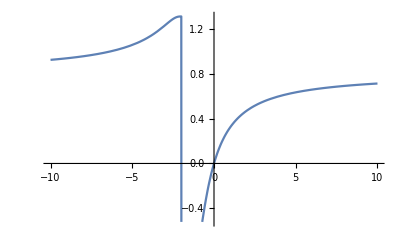

```mathematica
$Assumptions={η∈Reals, ζ∈Reals, -1<η<1, -1<ζ<2, η^2≠ζ^2};

(*Fundamental thm of calculus fails because primc is not continuous along the integration contour*)
primc=Integrate[intcplx, ρ]
D[primc, ρ] - intcplx //Simplify
Limit[primc, ρ-> Infinity] //FullSimplify
Limit[primc, ρ-> -1] //FullSimplify
Plot[primc /. η-> 0.2/. ζ-> 0.6, {ρ, -10, 10}]
```

```mathematica
(*Compute (∫^∞)_(-∞)intcplx dρ using residues. Construct a contour around the upper half plane and calculate the residues in this region.*) 
poles=Table[ρ/. Solve[Denominator[intcplx]==0, ρ][[i,1]], {i, 1, 4}]
residues=Table[Residue[intcplx, {ρ, poles[[i]]}], {i, 1, 4}];
residues=FullSimplify[residues]
(*The integrand vanishes at infinity*)
Limit[FullSimplify[intcplx /. ρ-> r E^(I θ)], r-> Infinity] ==0
(*Add the residues*)
Stotalbyresidues=FullSimplify[2 Pi I (residues[[2]]+residues[[4]])]
Stotalbyint=Integrate[intcplx, {ρ, -Infinity, Infinity}]
```

{(2 (-1-√(-ζ^2-2 ζ η-η^2)))/(1+ζ^2+2 ζ η+η^2),(2 (-1+√(-ζ^2-2 ζ η-η^2)))/(1+ζ^2+2 ζ η+η^2),(2 (-1-√(-ζ^2+2 ζ η-η^2)))/(1+ζ^2-2 ζ η+η^2),(2 (-1+√(-ζ^2+2 ζ η-η^2)))/(1+ζ^2-2 ζ η+η^2)}

{(ⅈ Abs[ζ+η])/(8 ζ η),-(ⅈ Abs[ζ+η])/(8 ζ η),-(ⅈ Abs[ζ-η])/(8 ζ η),(ⅈ Abs[ζ-η])/(8 ζ η)}

True

(π (-Abs[ζ-η]+Abs[ζ+η]))/(4 ζ η)

(π (-Abs[ζ-η]+Abs[ζ+η]))/(4 ζ η)

```mathematica
(*Investigation of the location of the Poles*)
Manipulate[ListPlot[N[Table[{{Re[poles[[i]]], Im[poles[[i]]]}} /. {ζ-> ζr+I ζi,η-> ηr+ I ηi }, {i, 4}]], PlotLegends->Table[i, {i,4}], 
PlotStyle->PointSize[Large],
PlotRange->{{-5, 1},{ -2, 2}}], 
{ζr, -1, 1, 0.2}, {ζi, -1, 1, 0.2}, {ηr, -1, 1, 0.2},{ηi, -1, 1, 0.2}]
```

```mathematica
(*The integration contours add like they should*)
sr=Integrate[intcplx, {ρ, -1, Infinity}]
st=Stotalbyint
sc=Integrate[intcplx, {ρ, -1, -Infinity}]
st-sr+sc ==0 //Simplify
```

((-ζ+η) ArcTan[ζ-η]+(ζ+η) ArcTan[ζ+η])/(2 ζ η)

(π (-Abs[ζ-η]+Abs[ζ+η]))/(4 ζ η)

-(-π Abs[ζ-η]+π Abs[ζ+η]+2 (ζ-η) ArcTan[ζ-η]-2 (ζ+η) ArcTan[ζ+η])/(4 ζ η)

True

```mathematica
(*the anti-derivative is discontinuous along (-∞,-1), which is why is cannot be used to integrate over it*)
Manipulate[Plot[{Re[primc]/. {ζ-> ζr+I ζi,η-> ηr+ I ηi }, Im[primc]/. {ζ-> ζr+I ζi,η-> ηr+ I ηi }} , {ρ, -5, 5}, PlotStyle->{Blue,Red}], 
{ζr, -1, 1, 0.2}, {ζi, -1, 1, 0.2}, {ηr, -1, 1, 0.2},{ηi, -1, 1, 0.2}]
```

```mathematica
(*Numerical and exact agree*)
Scplx[ζ_,η_]:=Evaluate[sc (1+(η+ζ)^2)/2]
Scplx[0.2,0.6]
SNcplx[0.2,0.6]
```

-0.822488

-0.822488

```mathematica
(*Numeric agrees for ζ=0*)
SNreal[10^(-10),0.5]
Sreal[10^(-10),0.5]
```

-2.15912

-2.15912

### More intelligent talk about integrating

True

-Graphics3D-

-Graphics3D-

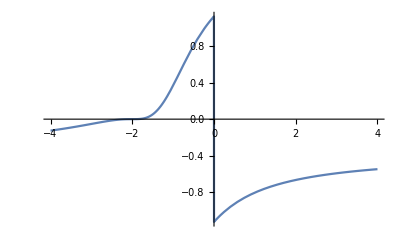

```mathematica
$Assumptions={};

(*However, we can do a better job, and find a function whose derivative is g[ρ]=intcplx and is continuous along (-∞,-1) for η and ζ real*)
altprim[ρ_]:=-((-ζ+η) ArcCot[((ζ-η) ρ)/(2+ρ)]+(ζ+η) ArcCot[((ζ+η) ρ)/(2+ρ)])/(4 ζ η)
Simplify[D[altprim[ρ],ρ]-intcplx]==0
Plot3D[Re[altprim[ρ]] /. ζ-> 0.3 /. η-> 0.7 /. ρ-> ρr+I ρi, {ρr, -3, 1}, {ρi, -2, 2}]
Plot3D[Im[altprim[ρ]] /. ζ-> 0.3 /. η-> 0.7 /. ρ-> ρr+I ρi, {ρr, -3, 1}, {ρi, -2, 2}]
Plot[altprim[ρ]/. ζ-> 0.3 /. η-> 0.7, {ρ, -4, 4}]
```

```mathematica
(*The integral naturally evaluates to*)
SCcot = FullSimplify[-altprim[-1] +Limit[altprim[ρ], ρ-> Infinity]]
```

((ζ-η) ArcCot[ζ-η]-(ζ+η) ArcCot[ζ+η])/(2 ζ η)

```mathematica
(*This has an easy ζ -> 0 limit*)
FullSimplify[Limit[SCcot(1+(η+ζ)^2),  ζ-> 0]]
```

1-((1+η^2) ArcCot[η])/η

```mathematica
(*They are the same if η and ζ are reals*)
FullSimplify[sc-SCcot, {η∈Reals, ζ∈Reals}]==0
(*This is due to the following identity*)
FullSimplify[2 x ArcTan[x]+2x ArcCot[x]-Pi Abs[x], x∈Reals]==0
```

True

True

```mathematica
(*This is also the same as the action used above*)
Simplify[SCcot(1+(ζ+η)^2)/2-ComplexUnitonAction[ζ,η]]==0
```

True

## Old and/or possibly wrong

### θ-formulations

```mathematica
inputrealth=-2 k t^(-1) Sin[θ]Sqrt[1+(η-ζ)^2 Sin[θ]^2]/(1+ζ^2+η^2+2ζ η Cos[2 θ]) ;
intrealth=inputrealth t/ (2 k) *(1+(η+ζ)^2);
SNθ[z_, e_]:=NIntegrate[intrealth/.{ζ-> z, η-> e} , {θ, 0, Pi}]
S1[η_]:=1+(1/η+η) ArcTan[η]
SE2[ζ_, η_]:=1/(2  ζ η)(1+(η+ζ)^2)(2 (ζ-η) ArcTan[ζ-η]+ⅈ (ζ+η) (Log[-(8 ζ η (ζ+ⅈ ζ^2+2 √ζ √(1+(ζ-η)^2) √η+η-2 ⅈ ζ η+ⅈ η^2))/((ζ+η)^3 (1+ζ^2-2 ⅈ √ζ √(1+(ζ-η)^2) √η-2 ζ η+η^2))]-Log[(8 ⅈ ζ η (ζ^2+ζ (ⅈ-2 η)+2 ⅈ √ζ √(1+(ζ-η)^2) √η+η (ⅈ+η)))/((ζ+η)^3 (1+ζ^2+2 ⅈ √ζ √(1+(ζ-η)^2) √η-2 ζ η+η^2))]))
```

```mathematica
SR=1/(4 ζ η)ⅈ (1+(ζ+η)^2) ((ζ-η) Log[2+2 ⅈ ζ-2 ⅈ η]+(-ζ+η) Log[2-2 ⅈ ζ+2 ⅈ η]+(ζ+η) (Log[(8 ⅈ ζ η (ζ^2+ζ (ⅈ-2 η)+η (ⅈ+η)+2 ⅈ √ζ √η √(1+ζ^2-2 ζ η+η^2)))/((ζ+η)^3 √(1+ζ^2-2 ζ η+η^2) (2 ⅈ √ζ √η+√(1+ζ^2-2 ζ η+η^2)))]-Log[-(8 ζ η (ζ+ⅈ ζ^2+η-2 ⅈ ζ η+ⅈ η^2+2 √ζ √η √(1+ζ^2-2 ζ η+η^2)))/((ζ+η)^3 √(1+ζ^2-2 ζ η+η^2) (-2 ⅈ √ζ √η+√(1+ζ^2-2 ζ η+η^2)))]));
FullSimplify[SR]
SR2[ζ_, η_]:=Evaluate[SR]
SR2[0.2,0.5]
SN[0.2,0.5]
SComplicated[ζ,η]/SR2[ζ,η] //FullSimplify
```

1/(4 ζ η)(-ⅈ+ζ+η) (ⅈ+ζ+η) (2 (-ζ+η) ArcTan[ζ-η]-ⅈ (ζ+η) (Log[-(8 ζ η (ζ+ⅈ ζ^2+2 √ζ √(1+(ζ-η)^2) √η+η-2 ⅈ ζ η+ⅈ η^2))/((ζ+η)^3 (1+ζ^2-2 ⅈ √ζ √(1+(ζ-η)^2) √η-2 ζ η+η^2))]-Log[(8 ⅈ ζ η (ζ^2+ζ (ⅈ-2 η)+2 ⅈ √ζ √(1+(ζ-η)^2) √η+η (ⅈ+η)))/((ζ+η)^3 (1+ζ^2+2 ⅈ √ζ √(1+(ζ-η)^2) √η-2 ζ η+η^2))]))

-13.8499+0. ⅈ

2.53353

-((4 ⅈ ζ η SComplicated[ζ,η])/((1+(ζ+η)^2) (2 ⅈ (ζ-η) ArcTan[ζ-η]-(ζ+η) (Log[-(8 ζ η (ζ+ⅈ ζ^2+2 √ζ √(1+(ζ-η)^2) √η+η-2 ⅈ ζ η+ⅈ η^2))/((ζ+η)^3 (1+ζ^2-2 ⅈ √ζ √(1+(ζ-η)^2) √η-2 ζ η+η^2))]-Log[(8 ⅈ ζ η (ζ^2+ζ (ⅈ-2 η)+2 ⅈ √ζ √(1+(ζ-η)^2) √η+η (ⅈ+η)))/((ζ+η)^3 (1+ζ^2+2 ⅈ √ζ √(1+(ζ-η)^2) √η-2 ζ η+η^2))]))))

```mathematica
r=-(8 ζ η (ζ+ⅈ ζ^2+2 √ζ √(1+(ζ-η)^2) √η+η-2 ⅈ ζ η+ⅈ η^2))/((ζ+η)^3 (1+ζ^2-2 ⅈ √ζ √(1+(ζ-η)^2) √η-2 ζ η+η^2))
rb=r //. {ⅈ-> -ⅈ, Complex[0,-2]-> +2ⅈ}
SRt=1/(4 ζ η)(1+ζ^2+2 ζ η+η^2) (2 (-ζ+η) ArcTan[ζ-η] -ⅈ(ζ+η)(Log[t]-Log[ tb])) 
SRt-SR /.{t-> r, tb-> rb}//FullSimplify
```

-(8 ζ η (ζ+ⅈ ζ^2+2 √ζ √(1+(ζ-η)^2) √η+η-2 ⅈ ζ η+ⅈ η^2))/((ζ+η)^3 (1+ζ^2-2 ⅈ √ζ √(1+(ζ-η)^2) √η-2 ζ η+η^2))

-(8 ζ η (ζ-ⅈ ζ^2+2 √ζ √(1+(ζ-η)^2) √η+η+2 ⅈ ζ η-ⅈ η^2))/((ζ+η)^3 (1+ζ^2+2 ⅈ √ζ √(1+(ζ-η)^2) √η-2 ζ η+η^2))

((1+ζ^2+2 ζ η+η^2) (2 (-ζ+η) ArcTan[ζ-η]-ⅈ (ζ+η) (Log[t]-Log[tb])))/(4 ζ η)

0

```mathematica
rre=Simplify[ComplexExpand@Re[r],Arg[ζ]==Arg[η]==0]
rim=Simplify[ComplexExpand@Im[r],Arg[ζ]==Arg[η]==0]
rim/rre
```

-(8 ζ η (ζ+ζ^3+η-ζ^2 η-ζ η^2+η^3+2 √(ζ η (1+ζ^2-2 ζ η+η^2))))/((ζ+η)^3 (1+ζ^2-2 ζ η+η^2) (1+ζ^2+2 ζ η+η^2))

-(8 ζ η (ζ+ζ^3+η-ζ^2 η-ζ η^2+η^3+2 √(ζ η (1+ζ^2-2 ζ η+η^2))))/((ζ+η)^2 (1+ζ^2-2 ζ η+η^2) (1+ζ^2+2 ζ η+η^2))

ζ+η

```mathematica
Snewest[ζ_,η_]:=1/(4 ζ η)(1+ζ^2+2 ζ η+η^2) (2 (-ζ+η) ArcTan[ζ-η] +4(ζ+η)ArcTan[ζ+η])
Abs[Snewest[0.2,0.5]]
```

5.71847

### Matching with actual data

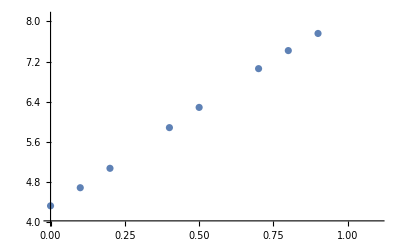

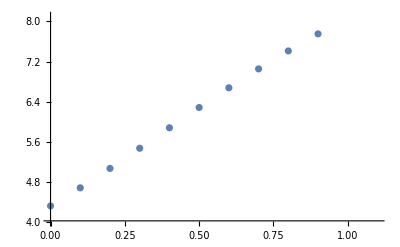

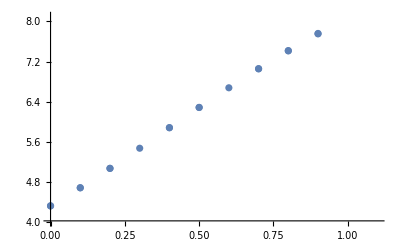

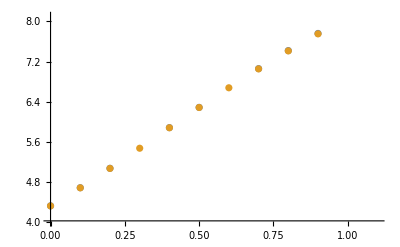

```mathematica
(*Only For PlotDataRange*)
min[j_]:=SetPrecision[Min[Select[ComplexExpand@Re[PadePoles[j]], NonNegative]],4]
p1=ListPlot[Table[{(j-1)/10,min[j]},{j, 1, 10}], PlotRange->{{0,1.1}, {4, 8.1}}]
p2=ListPlot[Table[{(i-1)/10,2 SN2[DeformationProbes[[i,1]]+10^-5, DeformationProbes[[i,2]]+10^-5]},{i, 1, 10}], PlotRange->{{0,1.1}, {4, 8.1}}]
Show[p1, p2]
p2=ListPlot[{Table[{(j-1)/10,min[j]},{j, 1, 10}],Table[{(i-1)/10,2 SN2[DeformationProbes[[i,1]]+10^-5, DeformationProbes[[i,2]]+10^-5]},{i, 1, 10}]}, PlotRange->{{0,1.1}, {4, 8.1}} ]
```

### Cplx Uniton

```mathematica
L3c=(4 (-1+f[w] f[z])^2 f'[w] f'[z])/((1+(ζ-η)^2+f[w] f[z] (2 (-1+(ζ-η)^2)+(1+(ζ-η)^2) f[w] f[z])) (1+(ζ+η)^2+f[w] f[z] (2 (-1+ζ+η) (1+ζ+η)+(1+(ζ+η)^2) f[w] f[z])));
Linr=Simplify[L3c/(f'[w]f'[z]) /. f[w]-> r^2/f[z]]r
SNcplx[z_, e_]:=NIntegrate[Evaluate[Linr](1+(ζ+η)^2)/2 /. ζ-> z /. η-> e, {r, 0, Infinity}]
Cplx1[η_]:=(1-(η+η^-1)(ArcCot[η]))
SNcplx[0.2,0.6] 
SNcplx[0.6, 0]
Cplx1[0.6]/2
```

(4 r (-1+r^2)^2)/((1+2 r^2 (-1+(ζ-η)^2)+r^4 (1+(ζ-η)^2)+(ζ-η)^2) (1+(ζ+η)^2+2 r^2 (-1+ζ+η) (1+ζ+η)+r^4 (1+(ζ+η)^2)))

0.822488

0.66776

-0.66776

```mathematica
Cplx1[0]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
ExactCplxUntion=Integrate[Evaluate[Linr](1+(ζ+η)^2)/2 , {r, 0, Infinity}]
```

ConditionalExpression[1/(64 (ζ-η) (ζ+η))(1+(ζ+η)^2) ((-ⅈ+ζ-η) (1/ζ(ⅈ+ζ+η) (ⅈ (Log[(-ⅈ+ζ-η)/(ⅈ+ζ-η)]-Log[(ⅈ+ζ+η)/(-ⅈ+ζ+η)])+(ⅈ (8 ⅈ ζ (-1+ζ^2-η^2) Log[(ⅈ+ζ+η)/(-ⅈ+ζ+η)]+(1-2 ⅈ ζ-ζ^2+η^2)^2 Log[(1+2 ⅈ ζ-ζ^2+η^2)/(1-2 ⅈ ζ-ζ^2+η^2)]))/((ⅈ-ζ+η)^2 (ⅈ+ζ+η)^2)-(2 (4 ζ Log[(ⅈ+ζ+η)/(-ⅈ+ζ+η)]+(2 ζ-ⅈ ζ^2+ⅈ (1+η^2)) Log[(1+2 ⅈ ζ-ζ^2+η^2)/(1-2 ⅈ ζ-ζ^2+η^2)]))/((-ⅈ+ζ-η) (ⅈ+ζ+η)))-1/η(-ⅈ+ζ+η) (ⅈ (Log[(-ⅈ+ζ-η)/(ⅈ+ζ-η)]-Log[(-ⅈ+ζ+η)/(ⅈ+ζ+η)])-(2 (4 η Log[(-ⅈ+ζ+η)/(ⅈ+ζ+η)]-ⅈ (ζ^2-(-ⅈ+η)^2) Log[((-ⅈ+ζ-η) (ⅈ+ζ+η))/(ζ^2-(-ⅈ+η)^2)]))/((-ⅈ+ζ-η) (-ⅈ+ζ+η))+(8 η (-1-ζ^2+η^2) Log[(-ⅈ+ζ+η)/(ⅈ+ζ+η)]+ⅈ (ζ^2-(-ⅈ+η)^2)^2 Log[((-ⅈ+ζ-η) (ⅈ+ζ+η))/(ζ^2-(-ⅈ+η)^2)])/((1+2 ⅈ ζ-ζ^2+η^2)^2)))+4 (ⅈ+ζ-η) (-1/(4 ζ)(-ⅈ+ζ+η) (ⅈ (Log[(ⅈ+ζ-η)/(-ⅈ+ζ-η)]-Log[(-ⅈ+ζ+η)/(ⅈ+ζ+η)])+(2 (4 ζ Log[(-ⅈ+ζ+η)/(ⅈ+ζ+η)]+ⅈ (-1-2 ⅈ ζ+ζ^2-η^2) Log[(1-2 ⅈ ζ-ζ^2+η^2)/(1+2 ⅈ ζ-ζ^2+η^2)]))/(ζ^2-(-ⅈ+η)^2)+(ⅈ (-8 ⅈ ζ (-1+ζ^2-η^2) Log[(-ⅈ+ζ+η)/(ⅈ+ζ+η)]+(1+2 ⅈ ζ-ζ^2+η^2)^2 Log[(1-2 ⅈ ζ-ζ^2+η^2)/(1+2 ⅈ ζ-ζ^2+η^2)]))/((ζ^2-(-ⅈ+η)^2)^2))-1/(4 η)(ⅈ+ζ+η) (-ⅈ (Log[(ⅈ+ζ-η)/(-ⅈ+ζ-η)]-Log[(ⅈ+ζ+η)/(-ⅈ+ζ+η)])-(2 (4 η Log[(ⅈ+ζ+η)/(-ⅈ+ζ+η)]+ⅈ (ζ^2-(ⅈ+η)^2) Log[(ζ^2-(-ⅈ+η)^2)/(ζ^2-(ⅈ+η)^2)]))/((ⅈ+ζ-η) (ⅈ+ζ+η))+(8 η (-1-ζ^2+η^2) Log[(ⅈ+ζ+η)/(-ⅈ+ζ+η)]-ⅈ (ζ^2-(ⅈ+η)^2)^2 Log[(ζ^2-(-ⅈ+η)^2)/(ζ^2-(ⅈ+η)^2)])/((ⅈ+ζ-η)^2 (ⅈ+ζ+η)^2)))),(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)])||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)])||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0)||(Im[ζ+η]==1+1/Re[(ζ+η)/(-ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0)||(Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0)||(Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0)||(Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0)||(Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0)||(Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0)||(Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0)||(Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0)||(Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0)||(Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0)||(Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0)||(Im[(ζ+η)/(ⅈ+ζ+η)]≠Re[1/(ⅈ+ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ+ζ-η)]&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Re[ζ-η]≠1/Im[(ζ-η)/(ⅈ-ζ+η)]&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0)||(1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0)||(1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(1/Re[(-ζ+η)/(ⅈ+ζ-η)]==1+Im[ζ-η]&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0)||(Re[ζ+η]≠1/Im[(ζ+η)/(ⅈ+ζ+η)]&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]==0&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0)||(Im[(ζ+η)/(-ⅈ+ζ+η)]+Re[1/(-ⅈ+ζ+η)]≠0&&Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)||(Im[1/(ⅈ+ζ-η)]+Re[(ζ-η)/(ⅈ+ζ-η)]≥0&&-Im[1/(-ⅈ+ζ-η)]-Re[(ζ-η)/(ⅈ-ζ+η)]≥0&&-Im[1/(-ⅈ+ζ+η)]+Re[(ζ+η)/(-ⅈ+ζ+η)]≥0&&Im[1/(ⅈ+ζ+η)]+Re[(ζ+η)/(ⅈ+ζ+η)]≥0)]

### Old And/or wrong

```mathematica
integrand1=-2 k t^(-1) Sin[θ]Sqrt[1+(η-ζ)^2 Sin[θ]^2]/(1+ζ^2+η^2+ζ η Cos[2 θ]/2) ;
integrand3=-2 k t^(-1) Sin[θ]Sqrt[1+(η-ζ)^2 Sin[θ]^2]/(1+(ζ+η)^2+ζ η Cos[ θ]) ;
SI1=-integrand1*t/ (2 k) *(1+(η+ζ)^2);
SN1[z_, e_]:=NIntegrate[SI1 /.{ζ-> z, η-> e} , {θ, 0, Pi}]
SE1[ζ_,η_]:=(2((ζ-η) ArcTan[ζ-η]-(√(2 ζ^4-3 ζ^3 η+2 ζ^2 (1+η^2)-ζ η (2+3 η^2)+2 (η^2+η^4)) ArcTan[(√(2 ζ^4-3 ζ^3 η+2 ζ^2 (1+η^2)-ζ η (2+3 η^2)+2 (η^2+η^4)))/(√(2+2 ζ^2-ζ η+2 η^2))])/(√(2+2 ζ^2-ζ η+2 η^2))))/(ζ η)(1+(η+ζ)^2);
```

### Result of the Real Uniton Integral

```mathematica
Result=ConditionalExpression[1/(4 ζ η)ⅈ (1+(ζ+η)^2) ((ζ-η) Log[2+2 ⅈ ζ-2 ⅈ η]+(-ζ+η) Log[2-2 ⅈ ζ+2 ⅈ η]+(ζ+η) (Log[(8 ⅈ ζ η (ζ^2+ζ (ⅈ-2 η)+η (ⅈ+η)+2 ⅈ √ζ √η √(1+ζ^2-2 ζ η+η^2)))/((ζ+η)^3 √(1+ζ^2-2 ζ η+η^2) (2 ⅈ √ζ √η+√(1+ζ^2-2 ζ η+η^2)))]-Log[-(8 ζ η (ζ+ⅈ ζ^2+η-2 ⅈ ζ η+ⅈ η^2+2 √ζ √η √(1+ζ^2-2 ζ η+η^2)))/((ζ+η)^3 √(1+ζ^2-2 ζ η+η^2) (-2 ⅈ √ζ √η+√(1+ζ^2-2 ζ η+η^2)))])),((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2∉Reals||Re[(ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2]<0||√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals||Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]>√2)&&((Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0))&&((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2∉Reals||Re[(ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2]<0||√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals||Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]>√2)&&((Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≥√2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)]≤0&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0)||(Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]>2&&Re[√(2-(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≥2&&Re[(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η)]<-2&&Re[√(2+(√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))]≤0&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)∉Reals&&√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2)≠0&&√((2 ζ η-√(-ζ η (1+ζ^2-2 ζ η+η^2)))/(ζ η))≠0))]
```

ConditionalExpression[(ⅈ (1+1) ((ζ-η) Log[2+2 ⅈ ζ-2 ⅈ η]+(-ζ+η) Log[1]+(ζ+η) (Log[(8 ⅈ ζ η (ζ^2+2+2 ⅈ √ζ √η √1))/((ζ+η)^3 √(1+ζ^2-1+η^2) (2 ⅈ √ζ √η+√(1+3+η^2)))]-Log[-1])))/(4 ζ η),((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-2 ζ η+η^2)))/(ζ-η)^2∉ℝ||Re[1/(ζ-η)^2]<0||√(1/1^2)∉ℝ||Re[√((ζ^2-2 ζ η+η^2-√((ζ-η)^2 (1+ζ^2-1+η^2)))/(ζ-η)^2)]>√2)&&(1)&&(1)&&(1)]
 |  |  |  |